```mathematica
UNET`$Verbose=True;
<<UNET`
```

--------------------------------------

Loading UNET` with version number 1.3.0

--------------------------------------

Defined packages and functions to be loaded are:

- UNET`UnetCore` with functions:

{AddLossLayer,AugmentTrainData,BlockType,BrierLossLayer,ClassDecoder,ClassEncoder,ClassScale,DiceSimilarity,DiceSimilarityClass,DropOutRate,MakeChannelImage,MakeClassImage,MakeDifferenceImage,MakeDiffLabel,MakeNetPlots,MakeUNET,NetLossLayers,NetParameters,NumberRowItems,RandomizeSplit,RotateFlip,ShowChannelClassData,SoftDiceLossLayer,SplitRatios,SplitTrainData,StepSize,TrainUNET,VisualizeUNET2D}

- UNET`UnetSupport` with functions:

{CreateImage1,CreateImage2,CreateImage3,CreateImage4,MakeTestImages}

--------------------------------------

Removing all local and global definitions of:

- UNET`UnetCore`

- UNET`UnetSupport`

--------------------------------------

Loading and protecting all definitions of:

- UNET`UnetCore`

- UNET`UnetSupport`

## Generated Data

### Show 2D UNET

```mathematica
dim={112,112};
```

```mathematica
MakeUNET[1,8,12,dim,DropOutRate->.5,BlockType->"UNET"]
```

NetGraph[<>]

```mathematica
MakeUNET[1,8,12,dim,DropOutRate->.5,BlockType->"UResNet"]
```

NetGraph[<>]

```mathematica
MakeUNET[1,8,12,dim,DropOutRate->.5,BlockType->"ResNet"]
```

NetGraph[<>]

```mathematica
MakeUNET[1,8,{12,1},dim,DropOutRate->.5,BlockType->"UDenseNet"]
```

NetGraph[<>]

```mathematica
MakeUNET[1,8,{12,1},{128,128},DropOutRate->.5,BlockType->"DenseNet"]
```

NetGraph[<>]

### Show 3D UNET

```mathematica
dim={32,112,112};
```

```mathematica
MakeUNET[1,8,12,dim,DropOutRate->.5,BlockType->"UNET"]
```

NetGraph[<>]

```mathematica
MakeUNET[1,8,12,dim,DropOutRate->.5,BlockType->"UResNet"]
```

NetGraph[<>]

```mathematica
MakeUNET[1,8,12,dim,DropOutRate->.5,BlockType->"ResNet"]
```

NetGraph[<>]

```mathematica
MakeUNET[1,8,{12,1},dim,DropOutRate->.5,BlockType->"UDenseNet"]
```

NetGraph[<>]

```mathematica
MakeUNET[1,8,{12,1},{128,128},DropOutRate->.5,BlockType->"DenseNet"]
```

NetGraph[<>]

### Describe UNET

```mathematica
style={Bold,TextAlignment->Center,FontFamily->"Helvetica"};
lab=Style[#,style]&/@{"n or (n, r)", "Unet", "UResNet", "ResNet", "UDenseNet", "DenseNet"};
```

```mathematica
CountConv=Count[Head/@Information[#,"LayersList"],ConvolutionLayer]&;
```

```mathematica
(*parameters*)
dim2D={112,112};
dim3D={32,112,112};
{nchan,nclass}={4,8};

dep={8,16,24,32,48,64};
depD=Thread[{dep,1}];
par=Table[ToString[dep[[i]]]<>" or ("<>ToString[depD[[i,1]]]<>","<>ToString[depD[[i,2]]]<>")",{i,1,Length[dep]}];
```

```mathematica
(*2D UNET generation*)
par2D=Table[
nets2D=MapThread[MakeUNET[nchan,nclass, #2[[i]],dim2D,BlockType->#1 ]&,{{"UNET","UResNet","ResNet","UDenseNet","DenseNet"},{dep,dep,dep,depD,depD}}];
Flatten@{par[[i]],Information[#,"ArraysTotalElementCount"]&/@nets2D}
,{i,1,Length[dep]}];

tab1=Column[{Style["2D Nets - Numer of Array Elementes",style],TableForm[par2D,TableHeadings->{None,lab},TableAlignments->Right]},Alignment->Center];
```

```mathematica
(*3D UNET generation*)
par3D=Table[nets3D=MapThread[MakeUNET[nchan,nclass, #2[[i]],dim3D,BlockType->#1 ]&,{{"UNET","UResNet","ResNet","UDenseNet","DenseNet"},{dep,dep,dep,depD,depD}}];
Flatten@{par[[i]],Information[#,"ArraysTotalElementCount"]&/@nets3D}
,{i,1,Length[dep]}];

tab2=Column[{Style["3D Nets - Numer of Array Elementes",style],TableForm[par3D,TableHeadings->{None,lab},TableAlignments->Right]},Alignment->Center];
```

```mathematica
Information[nets2D[[1]],"LayersList"]
```

```mathematica
layers2D=ToString[CountConv[#]]&/@nets2D;
layers3D=ToString[CountConv[#]]&/@nets3D;
layers=Column[{Style["Number of convolution layers",style],Style["1)  UNet: "<>layers2D[[1]]<>"    2)  UResNet: "<>layers2D[[2]]<>
"    3)  ResNet: "<>layers2D[[3]]<>"    4)  UDenseNet: "<>layers2D[[4]]<>"    5)  DenseNet: "<>layers2D[[5]],style]},Alignment->Center];
```

```mathematica
Column[{layers,"",tab1,"",tab2},Alignment->Center]
```

Number of convolution layers
1)  UNet: 23    2)  UResNet: 23    3)  ResNet: 32    4)  UDenseNet: 34    5)  DenseNet: 59

2D Nets - Numer of Array Elementes
n or (n, r) | Unet | UResNet | ResNet | UDenseNet | DenseNet
8 or (8,1) | 456736 | 235064 | 258696 | 16272 | 22360
16 or (16,1) | 1817656 | 933096 | 1023880 | 61720 | 84008
24 or (24,1) | 4082768 | 2094104 | 2295560 | 136352 | 184952
32 or (32,1) | 7252072 | 3718088 | 4073736 | 240168 | 325192
48 or (48,1) | 16303256 | 8354984 | 9149576 | 535352 | 723560
64 or (64,1) | 28971208 | 14843784 | 16251400 | 947272 | 1279112

3D Nets - Numer of Array Elementes
n or (n, r) | Unet | UResNet | ResNet | UDenseNet | DenseNet
8 or (8,1) | 1339744 | 676568 | 416904 | 44496 | 50584
16 or (16,1) | 5348536 | 2698536 | 1656968 | 173464 | 195752
24 or (24,1) | 12026384 | 6065912 | 3720200 | 386912 | 435512
32 or (32,1) | 21373288 | 10778696 | 6606600 | 684840 | 769864
48 or (48,1) | 48074264 | 24240488 | 14848904 | 1534136 | 1722344
64 or (64,1) | 85451464 | 43083912 | 26383880 | 2721352 | 3053192

### Examples of Test Data

```mathematica
{data,label}=CreateImage1[];
Flatten@{MakeChannelImage[data],Image[label]}
```

{-Graphics-,-Graphics-}

```mathematica
{data,label}=CreateImage2[];
Flatten@{MakeChannelImage[data],MakeClassImage[label]}
```

{-Graphics-,-Graphics-}

```mathematica
{data,label}=CreateImage3[];
Flatten@{MakeChannelImage[data],MakeClassImage[label,{1,4}]}
```

{-Graphics-,-Graphics-}

```mathematica
{data,label}=CreateImage4[];
Flatten@{MakeChannelImage[data],MakeClassImage[label,{1,4}]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Test Cases 1: 1 channel - 1 classes

```mathematica
(*make test data*)
{data1,label1}=MakeTestImages[100,1];
```

```mathematica
(*split the data*)
{train1,valid1,testData1,testLabel1,order1}=SplitTrainData[data1,label1];
```

Nuber of Samples in each set: {70,20,10}

Dimensions data: {100,1,128,128} - Dimensions label: {100,128,128}

```mathematica
(*visualize the test data*)
ShowChannelClassData[testData1,testLabel1, NumberRowItems->3,MakeDifferenceImage->False,StepSize->2]
```

channels: 1 - classes: 1 - Dimensions :{128,128}

Evaluating test data

DICE per class: {1→0.999}

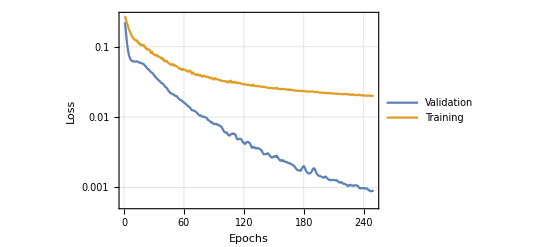
{-Graphics-,-Graphics-}

```mathematica
(*train the net*)
{{net1,trained1,netTrained1},{result1,iou1}}=TrainUNET[train1,valid1,{testData1,testLabel1},
TargetDevice->{"GPU",1},MaxTrainingRounds->250,NetParameters->4,DropOutRate->.5,BatchSize->32];
MakeNetPlots[trained1]
```

```mathematica
(*visualize the layers of the net*)
VisualizeUNET2D[testData1,netTrained1]
```

```mathematica
(*visualize the test data witout diff image*)
ShowChannelClassData[testData1,testLabel1,result1, NumberRowItems->3,MakeDifferenceImage->False,StepSize->1]
```

```mathematica
(*visualize the test data with diff image*)
ShowChannelClassData[testData1,testLabel1,result1, NumberRowItems->3,MakeDifferenceImage->True,StepSize->1]
```

### Test Case 2: 1 channel - 2 classes

```mathematica
(*make test data*)
{data2,label2}=MakeTestImages[100,2];
```

```mathematica
(*split the data*)
{train2,valid2,testData2,testLabel2,order}=SplitTrainData[data2,label2];
```

Nuber of Samples in each set: {70,20,10}

Dimensions data: {100,1,128,128} - Dimensions label: {100,128,128}

channels: 1 - classes: 2 - Dimensions :{128,128}

Evaluating test data

DICE per class: {1→0.999,2→0.991}

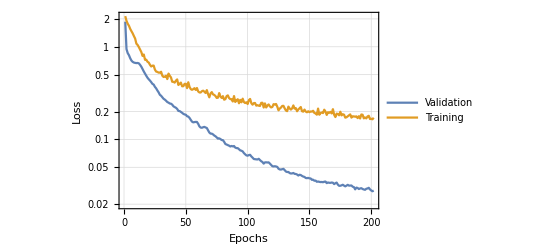
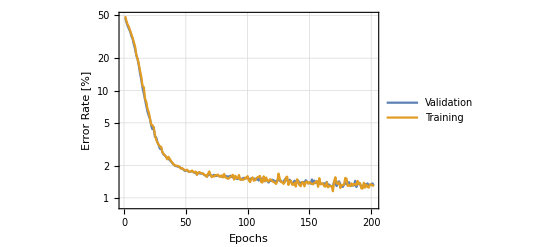

```mathematica
(*train the net*)
{{net2,trained2,netTrained2},{result2,iou2}}=TrainUNET[train2,valid2,{testData2,testLabel2},BatchSize->32,
TargetDevice->{"GPU",1},MaxTrainingRounds->250,NetParameters->4,DropOutRate->0.5,WorkingPrecision->"Mixed",PerformanceGoal->"TrainingMemory"];
MakeNetPlots[trained2]
```

```mathematica
(*visualize the layers of the net*)
VisualizeUNET2D[testData2,netTrained2]
```

```mathematica
(*visualize the test data witout diff image*)
ShowChannelClassData[testData2, testLabel2,result2, NumberRowItems->3,MakeDifferenceImage->True,StepSize->1]
```

### Test Case 3: 1 channel - 4 classes

```mathematica
(*make test data*)
{data3,label3}=MakeTestImages[100,3];
```

```mathematica
(*data augmentation, increase the data by flipping and rotating*)
(*visualize the flips and rotations*)
data3R=RotateFlip[data3[[1;;2]]];
label3R=RotateFlip[label3[[1;;2]]];
ShowChannelClassData[data3R,label3R, NumberRowItems->4,MakeDifferenceImage->False,StepSize->1,ImageSize->200]
```

```mathematica
(*split the data*)
{train3,valid3,testData3,testLabel3,order3}=SplitTrainData[data3,label3,AugmentTrainData->True];
```

Dimensions data: {100,1,128,128} - Dimensions label: {100,128,128}

Nuber of Samples in each set: {70,20,10}

Nuber of Samples in each set afeter augmentation: {560,160,10}

```mathematica
(*train the net*)
{{net3,trained3,netTrained3},{result3,iou3}}=TrainUNET[train3,valid3,{testData3,testLabel3},BatchSize->32,
TargetDevice->{"GPU",1},MaxTrainingRounds->100,NetParameters->8,BlockType->"ResNet",DropOutRate->0.5];
```

channels: 1 - classes: 4 - Dimensions :{128,128}

Evaluating test data

DICE per class: {1→0.998,2→0.959,3→0.974,4→0.964}

```mathematica
(*visualize the layers of the net*)
VisualizeUNET2D[testData3,netTrained3]
```

```mathematica
(*visualize the test data witout diff image*)
ShowChannelClassData[testData3, testLabel3, result3, NumberRowItems->3,MakeDifferenceImage->True,StepSize->1]
```

### Test Case 4 : 3 channels - 4 classes

```mathematica
(*make test data*)
{data4,label4}=MakeTestImages[100,4];
```

```mathematica
(*split the data*)
{train4,valid4,testData4,testLabel4,order4}=SplitTrainData[data4,label4];
```

Dimensions data: {100,3,128,128} - Dimensions label: {100,128,128}

Nuber of Samples in each set: {70,20,10}

channels: 3 - classes: 4 - Dimensions :{128,128}

Evaluating test data

DICE per class: {1→1.,2→0.982,3→1.,4→0.957}

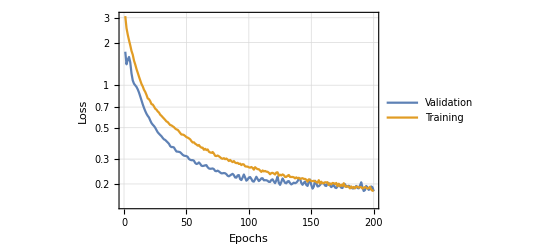
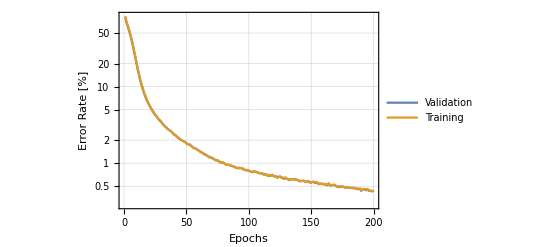

```mathematica
(*train the net*)
{{net4,trained4,netTrained4},{result4,iou4}}=TrainUNET[train4,valid4,{testData4,testLabel4},BatchSize->64,
TargetDevice->{"GPU",1},MaxTrainingRounds->200,NetParameters->16,
BlockType->"ResNet",DropOutRate->0.5,WorkingPrecision->"Mixed",PerformanceGoal->{"TrainingMemory","TrainingSpeed"}];
MakeNetPlots[trained4]
```

```mathematica
(*visualize the layers of the net*)
VisualizeUNET2D[testData4,netTrained4]
```

```mathematica
(*visualize the test data witout diff image*)
ShowChannelClassData[testData4, testLabel4, result4, NumberRowItems->2,MakeDifferenceImage->True,StepSize->1,ImageSize->650]
```

### Test Case 5 - same as 4 with animation

```mathematica
{data5,label5}=MakeTestImages[100,4];
```

```mathematica
{train5,valid5,testData5,testLabel5,order}=SplitTrainData[data5,label5];
```

Dimensions data: {100,3,128,128} - Dimensions label: {100,128,128}

Nuber of Samples in each set: {70,20,10}

```mathematica
(*choose a nice image*)
MakeChannelImage/@testData5
```

{{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}

```mathematica
im=6;nchan=Max[testLabel5];solutions={};
imChan=First@MakeChannelImage[testData5[[im,{1}]]];
(*The monitoring function*)
monitor=AppendTo[solutions,ClassDecoder[NetExtract[#Net,"net"][testData5[[im]],TargetDevice->"GPU"],nchan]]&;

(*train the net with monitor function*)
{{net,trained,netTrained},{result,iou}}=TrainUNET[train5,valid5,{testData5,testLabel5},BatchSize->32,
 TargetDevice->{"GPU",1},MaxTrainingRounds->200,NetParameters->16,DropOutRate->.5,NetLossLayers->All,
BlockType->"ResNet",TrainingProgressFunction->{monitor,"Interval"->Quantity[1,"Rounds"]}];
```

channels: 3 - classes: 4 - Dimensions :{128,128}

```mathematica
(*make the animation images*)
solIm=ColorReplace[MakeClassImage[#,{1,4}],ColorData["Rainbow"][0]]&/@solutions;
anim=Table[Show[ImageCompose[imChan,{sol,.5}],ImageSize->500],{sol,solIm}];

(*play the animatin*)
Animate[im,{im,anim}]
```

```mathematica
Export["anim.gif",anim,"DisplayDuration"->.2,"AnimationRepetitions"->Infinity]
```

```mathematica
MeanSurfaceDistance[res_,label_]:=Block[{resS,labS,posR,posL,m,pR,pL,mat,msd,lpR,lpL},
(*Split the segmentations*)
resS=SplitSegmentations[res][[1]];
labS=SplitSegmentations[label][[1]];
(*Get the posisitons of the edge voxels*)
posR=aa=Map[Position[m=ArrayPad[#,1];m1=m-Erosion[m,1],1]&,resS,{2}];
posL=bb=Map[Position[m=ArrayPad[#,1];m2=m-Erosion[m,1],1]&,labS,{2}];
(*calculate the MSD for each point for ech ROI*)
msd=MapThread[(
pR=#;pL=#2;
lpR=Length[pR];lpL=Length[pL];
If[lpR==0||lpL==0,
Missing,
msd=ParallelMap[Norm[Nearest[pL,#,1][[1]]-#]&,pR];
Mean[N[msd]]
]
)&,{posR,posL},2];

Mean[DeleteCases[#,Missing]]&/@Transpose[msd]
]
```